# Testing out DMFormFactor functions

```mathematica
SetDirectory["/home/farmer/mathematica/DMFormFactor_13086288"]
```

/home/farmer/mathematica/DMFormFactor_13086288

```mathematica
<<"v6/dmformfactor-V6.m";
```

Welcome to DMFormFactor version 1.1.

Functions are SetCoeffsNonrel, SetCoeffsRel, SetCoeffsNucl, ZeroCoeffs, SetJChi, SetMchi, SetIsotope, SetHALO, SetHelm, TransitionProbability, ResponseNucl, DiffCrossSection, ApproxTotalCrossSection, and EventRate.

## Event rate

Model setup

```mathematica
(* Model Setup *)
SetJChi[1/2](* WIMP spin *)
SetMChi[MWIMP GeV] (* WIMP mass in GeV *)
Xe131filename="default";  (* nuclear density matrix (using default density matrices) *)
bFM="default"; (* oscillation parameter (default: approximate formulae used) *)
SetIsotope[54,131,bFM,Xe131filename] (*[Z,A,bFM,filename]*)
ZeroCoeffs[];(*Reset all coefficients*)
SetCoeffsNonrel[1,c1p,"p"]
SetCoeffsNonrel[1,c1n,"n"]
SetCoeffsNonrel[2,c2p,"p"]
SetCoeffsNonrel[2,c2n,"n"]
SetCoeffsNonrel[3,c3p,"p"]
SetCoeffsNonrel[3,c3n,"n"]
SetCoeffsNonrel[4,c4p,"p"]
SetCoeffsNonrel[4,c4n,"n"]
SetCoeffsNonrel[5,c5p,"p"]
SetCoeffsNonrel[5,c5n,"n"]
SetCoeffsNonrel[6,c6p,"p"]
SetCoeffsNonrel[6,c6n,"n"]
SetCoeffsNonrel[7,c7p,"p"]
SetCoeffsNonrel[7,c7n,"n"]
SetCoeffsNonrel[8,c8p,"p"]
SetCoeffsNonrel[8,c8n,"n"]
SetCoeffsNonrel[9,c9p,"p"]
SetCoeffsNonrel[9,c9n,"n"]
SetCoeffsNonrel[10,c10p,"p"]
SetCoeffsNonrel[10,c10n,"n"]
SetCoeffsNonrel[11,c11p,"p"]
SetCoeffsNonrel[11,c11n,"n"]
SetCoeffsNonrel[12,c12p,"p"]
SetCoeffsNonrel[12,c12n,"n"]
SetCoeffsNonrel[13,c13p,"p"]
SetCoeffsNonrel[13,c13n,"n"]
SetCoeffsNonrel[14,c14p,"p"]
SetCoeffsNonrel[14,c14n,"n"]
SetCoeffsNonrel[15,c15p,"p"]
SetCoeffsNonrel[15,c15n,"n"]
(* Set non-zero NR EFT coefficient values *)
```

Getting default matrix...

Setting isotope to xenon-131.

Attempting to compute a recoil spectrum...

```mathematica
(* Parameters *)
mNucleon=0.938 GeV;
NT=1/(131 mNucleon);(*Number of target nuclei per detector mass*)
Centimeter=(10^13 Femtometer);
rhoDM=0.3GeV/Centimeter^3;(*Local dark matter density*)
ve=232 KilometerPerSecond;(*Earth's velocity in galactic rest frame*)
v0=220 KilometerPerSecond;(*Mean WIMP speed in galactic rest frame*)
vesc=550 KilometerPerSecond;
SetHalo["MBcutoff"];
```

```mathematica
dRdE=EventRate[NT,rhoDM,qGeV,ve,v0,vesc]
```

Your Lagrangian is

L_prot=(0.0000187399 (ⅈ q·S_χ)(v^⊥.(ⅈq×S_N)) c15p)/GeV^4+(0.0000187399 (S_χ·q)(S_N·q) c6p)/GeV^4+(0.0000175831 ⅈ S_N·q c10p)/GeV^3+(0.0000175831 ⅈ S_χ·q c11p)/GeV^3+(0.0000175831 (ⅈq×S_χ)·(S_N·v^⊥) c13p)/GeV^3+(0.0000175831 (ⅈ q·S_χ)(v^⊥·S_N) c14p)/GeV^3+(0.0000175831 ⅈ S_N·(q×v^⊥) c3p)/GeV^3+(0.0000175831 ⅈ S_χ·(q×v^⊥) c5p)/GeV^3+(0.0000175831 ⅈ S_χ.(S_N×q) c9p)/GeV^3+(0.0000164977 S_χ·(S_N×v^⊥) c12p)/GeV^2+(0.0000164977 1 c1p)/GeV^2+(0.0000164977 (v^⊥)^2 c2p)/GeV^2+(0.0000164977 S_χ·S_N c4p)/GeV^2+(0.0000164977 S_N·v^⊥ c7p)/GeV^2+(0.0000164977 S_χ·v^⊥ c8p)/GeV^2

L_neut=(0.0000187399 (ⅈ q·S_χ)(v^⊥.(ⅈq×S_N)) c15n)/GeV^4+(0.0000187399 (S_χ·q)(S_N·q) c6n)/GeV^4+(0.0000175831 ⅈ S_N·q c10n)/GeV^3+(0.0000175831 ⅈ S_χ·q c11n)/GeV^3+(0.0000175831 (ⅈq×S_χ)·(S_N·v^⊥) c13n)/GeV^3+(0.0000175831 (ⅈ q·S_χ)(v^⊥·S_N) c14n)/GeV^3+(0.0000175831 ⅈ S_N·(q×v^⊥) c3n)/GeV^3+(0.0000175831 ⅈ S_χ·(q×v^⊥) c5n)/GeV^3+(0.0000175831 ⅈ S_χ.(S_N×q) c9n)/GeV^3+(0.0000164977 S_χ·(S_N×v^⊥) c12n)/GeV^2+(0.0000164977 1 c1n)/GeV^2+(0.0000164977 (v^⊥)^2 c2n)/GeV^2+(0.0000164977 S_χ·S_N c4n)/GeV^2+(0.0000164977 S_N·v^⊥ c7n)/GeV^2+(0.0000164977 S_χ·v^⊥ c8n)/GeV^2

Warning: Implementation of O_2 discards v_N^2 piece.

Your event rate is

1/(GeV MWIMP^3)2.6053×10^-44 (646.112 ⅇ^(-67.4762 qGeV^2) (0.223035 qGeV^2 (3.83376×10^-9 c12p^2 MWIMP^2+4.3548×10^-9 c13p^2 MWIMP^2 qGeV^2) (0.0798479+0.605014 qGeV^2-53.138 qGeV^4+262.736 qGeV^6-0.0000142182 qGeV^8)^2+0.223035 qGeV^2 (3.83376×10^-9 c12n^2 MWIMP^2+4.3548×10^-9 c13n^2 MWIMP^2 qGeV^2) (0.516607-22.1809 qGeV^2+263.486 qGeV^4-1294.83 qGeV^6+1311.43 qGeV^8)^2+0.141988 qGeV^2 (3.83376×10^-9 c12n c12p MWIMP^2+4.3548×10^-9 c13n c13p MWIMP^2 qGeV^2) (-0.129591+4.58215 qGeV^2+62.3055 qGeV^4-4305.25 qGeV^6+64426.2 qGeV^8-436132. qGeV^10+1.28769×10^6 qGeV^12-1.08247×10^6 qGeV^14+0.0585786 qGeV^16)+(0.266447 GeV ((4.08598×10^-9 c4p c5p MWIMP^2)/GeV-(4.08598×10^-9 c8p c9p MWIMP^2)/GeV) qGeV^2+(7.20622×10^-14 c2p c3p (122.914 GeV+GeV MWIMP)^2 qGeV^4)/GeV^2) (0.00160907-0.274616 qGeV^2+5.35326 qGeV^4+188.744 qGeV^6-7857.19 qGeV^8+102543. qGeV^10-567802. qGeV^12+1.13687×10^6 qGeV^14-14.3099 qGeV^16+0.0000454276 qGeV^18)+(0.266447 GeV ((4.08598×10^-9 c4n c5p MWIMP^2)/GeV-(4.08598×10^-9 c8p c9n MWIMP^2)/GeV) qGeV^2+(7.20622×10^-14 c2p c3n (122.914 GeV+GeV MWIMP)^2 qGeV^4)/GeV^2) (0.0626746-12.4529 qGeV^2+816.667 qGeV^4-26193.6 qGeV^6+453298. qGeV^8-4.27212×10^6 qGeV^10+2.04296×10^7 qGeV^12-3.82971×10^7 qGeV^14-3.63158×10^6 qGeV^16+24.4556 qGeV^18)+(0.266447 GeV ((4.08598×10^-9 c4p c5n MWIMP^2)/GeV-(4.08598×10^-9 c8n c9p MWIMP^2)/GeV) qGeV^2+(7.20622×10^-14 c2n c3p (122.914 GeV+GeV MWIMP)^2 qGeV^4)/GeV^2) (0.00804988-1.39694 qGeV^2+30.5161 qGeV^4+767.591 qGeV^6-49133.4 qGeV^8+860740. qGeV^10-6.1233×10^6 qGeV^12+1.57859×10^7 qGeV^14-4.2049×10^6 qGeV^16+24.4556 qGeV^18)+(0.266447 GeV ((4.08598×10^-9 c4n c5n MWIMP^2)/GeV-(4.08598×10^-9 c8n c9n MWIMP^2)/GeV) qGeV^2+(7.20622×10^-14 c2n c3n (122.914 GeV+GeV MWIMP)^2 qGeV^4)/GeV^2) (0.31355-63.199 qGeV^2+4351.6 qGeV^4-157684. qGeV^6+3.26796×10^6 qGeV^8-3.79559×10^7 qGeV^10+2.25918×10^8 qGeV^12-5.50605×10^8 qGeV^14+9.9853×10^7 qGeV^16+1.33494×10^7 qGeV^18)+(201.935-21488.2 qGeV^2+888868. qGeV^4-1.84641×10^7 qGeV^6+2.11327×10^8 qGeV^8-1.3687×10^9 qGeV^10+4.91456×10^9 qGeV^12-8.96637×10^9 qGeV^14+6.45128×10^9 qGeV^16) (1.23666×10^-9 c3n^2 MWIMP^2 qGeV^4+0.0709941 qGeV^2 (0.0000619174 c12n MWIMP-0.0000703324 c15n MWIMP qGeV^2)^2)+2 (145.179-13580.4 qGeV^2+488429. qGeV^4-8.70932×10^6 qGeV^6+8.34711×10^7 qGeV^8-4.30669×10^8 qGeV^10+1.10482×10^9 qGeV^12-1.07444×10^9 qGeV^14+933.526 qGeV^16) (1.23666×10^-9 c3n c3p MWIMP^2 qGeV^4+0.0709941 qGeV^2 (0.0000619174 c12n MWIMP-0.0000703324 c15n MWIMP qGeV^2) (0.0000619174 c12p MWIMP-0.0000703324 c15p MWIMP qGeV^2))+(104.803-8490.45 qGeV^2+263668. qGeV^4-3.98191×10^6 qGeV^6+3.1089×10^7 qGeV^8-1.20073×10^8 qGeV^10+1.81321×10^8 qGeV^12-314.895 qGeV^14+0.000136721 qGeV^16) (1.23666×10^-9 c3p^2 MWIMP^2 qGeV^4+0.0709941 qGeV^2 (0.0000619174 c12p MWIMP-0.0000703324 c15p MWIMP qGeV^2)^2)+(0.559596-48.5209 qGeV^2+2053.49 qGeV^4-48572.5 qGeV^6+665153. qGeV^8-4.71895×10^6 qGeV^10+1.42707×10^7 qGeV^12-7.3766×10^6 qGeV^14+1.05877×10^6 qGeV^16) (-(1.44124×10^-13 c2n^2 (122.914 GeV+GeV MWIMP)^2 qGeV^4)/GeV^2+0.283977 qGeV^2 (3.83376×10^-9 c8n^2 MWIMP^2+4.3548×10^-9 c5n^2 MWIMP^2 qGeV^2))+2 (0.111856-9.37791 qGeV^2+352.965 qGeV^4-7196.74 qGeV^6+80309.1 qGeV^8-456971. qGeV^10+1.07816×10^6 qGeV^12-288545. qGeV^14+1.9461 qGeV^16) (-(1.44124×10^-13 c2n c2p (122.914 GeV+GeV MWIMP)^2 qGeV^4)/GeV^2+0.283977 qGeV^2 (3.83376×10^-9 c8n c8p MWIMP^2+4.3548×10^-9 c5n c5p MWIMP^2 qGeV^2))+(0.0223585-1.8104 qGeV^2+59.7764 qGeV^4-1012.75 qGeV^6+9223.45 qGeV^8-42699.9 qGeV^10+78901.5 qGeV^12-1.06781 qGeV^14+3.62403×10^-6 qGeV^16) (-(1.44124×10^-13 c2p^2 (122.914 GeV+GeV MWIMP)^2 qGeV^4)/GeV^2+0.283977 qGeV^2 (3.83376×10^-9 c8p^2 MWIMP^2+4.3548×10^-9 c5p^2 MWIMP^2 qGeV^2))+(-1092.61+136660. qGeV^2-6.69697×10^6 qGeV^4+1.67374×10^8 qGeV^6-2.3488×10^9 qGeV^8+1.91238×10^10 qGeV^10-8.93828×10^10 qGeV^12+2.25368×10^11 qGeV^14-2.6101×10^11 qGeV^16+8.70616×10^10 qGeV^18) (0.0000175831 c11n MWIMP qGeV^2 (0.0000619174 c12n MWIMP-0.0000703324 c15n MWIMP qGeV^2)+0.0000703324 c3n MWIMP qGeV^2 (0.0000619174 c1n MWIMP-(1.0246×10^-9 c2n (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP)))+(-788.171+88535.2 qGeV^2-3.83095×10^6 qGeV^4+8.34616×10^7 qGeV^6-1.00003×10^9 qGeV^8+6.69854×10^9 qGeV^10-2.38915×10^10 qGeV^12+3.83802×10^10 qGeV^14-1.44998×10^10 qGeV^16+12598.1 qGeV^18) (0.0000175831 c11n MWIMP qGeV^2 (0.0000619174 c12p MWIMP-0.0000703324 c15p MWIMP qGeV^2)+0.0000703324 c3p MWIMP qGeV^2 (0.0000619174 c1n MWIMP-(1.0246×10^-9 c2n (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP)))+(-766.296+87381.7 qGeV^2-3.85542×10^6 qGeV^4+8.50187×10^7 qGeV^6-1.02681×10^9 qGeV^8+6.95791×10^9 qGeV^10-2.58068×10^10 qGeV^12+4.78309×10^10 qGeV^14-3.44354×10^10 qGeV^16+12598.1 qGeV^18) (0.0000175831 c11p MWIMP qGeV^2 (0.0000619174 c12n MWIMP-0.0000703324 c15n MWIMP qGeV^2)+0.0000703324 c3n MWIMP qGeV^2 (0.0000619174 c1p MWIMP-(1.0246×10^-9 c2p (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP)))+(-552.779+55988.5 qGeV^2-2.15745×10^6 qGeV^4+4.09181×10^7 qGeV^6-4.1376×10^8 qGeV^8+2.23042×10^9 qGeV^10-5.88876×10^9 qGeV^12+5.71999×10^9 qGeV^14-7095.2 qGeV^16+0.00184509 qGeV^18) (0.0000175831 c11p MWIMP qGeV^2 (0.0000619174 c12p MWIMP-0.0000703324 c15p MWIMP qGeV^2)+0.0000703324 c3p MWIMP qGeV^2 (0.0000619174 c1p MWIMP-(1.0246×10^-9 c2p (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP)))+(0.0878436+9.96911 qGeV^2-264.17 qGeV^4-17861.1 qGeV^6+1.61079×10^6 qGeV^8-4.68721×10^7 qGeV^10+6.461×10^8 qGeV^12-4.27656×10^9 qGeV^14+1.11665×10^10 qGeV^16-4.34684×10^8 qGeV^18+4.29089×10^6 qGeV^20) (1.0887×10^-9 c10n^2 MWIMP^2 qGeV^2+1/16 (3.83376×10^-9 c4n^2 MWIMP^2+8.70959×10^-9 c4n c6n MWIMP^2 qGeV^2+4.94664×10^-9 c6n^2 MWIMP^2 qGeV^4-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c12n^2 MWIMP^2+4.3548×10^-9 c13n^2 MWIMP^2 qGeV^2)))+(0.00225524+0.106455 qGeV^2-12.073 qGeV^4-29.6556 qGeV^6+24984.9 qGeV^8-773389. qGeV^10+9.78397×10^6 qGeV^12-5.59042×10^7 qGeV^14+1.14708×10^8 qGeV^16-2.13056×10^6 qGeV^18+6.86271 qGeV^20) (1.0887×10^-9 c10n c10p MWIMP^2 qGeV^2+1/16 (3.83376×10^-9 c4n c4p MWIMP^2+8.70959×10^-9 c4p c6n MWIMP^2 qGeV^2+4.94664×10^-9 c6n c6p MWIMP^2 qGeV^4-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c12n c12p MWIMP^2+4.3548×10^-9 c13n c13p MWIMP^2 qGeV^2)))+(0.00225524+0.106455 qGeV^2-12.073 qGeV^4-29.6556 qGeV^6+24984.9 qGeV^8-773389. qGeV^10+9.78397×10^6 qGeV^12-5.59042×10^7 qGeV^14+1.14708×10^8 qGeV^16-2.13056×10^6 qGeV^18+6.86271 qGeV^20) (1.0887×10^-9 c10n c10p MWIMP^2 qGeV^2+1/16 (3.83376×10^-9 c4n c4p MWIMP^2+8.70959×10^-9 c4n c6p MWIMP^2 qGeV^2+4.94664×10^-9 c6n c6p MWIMP^2 qGeV^4-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c12n c12p MWIMP^2+4.3548×10^-9 c13n c13p MWIMP^2 qGeV^2)))+(0.0000578995-0.00110472 qGeV^2+0.145001 qGeV^4-23.9866 qGeV^6+1134.14 qGeV^8-23107.7 qGeV^10+224088. qGeV^12-984096. qGeV^14+1.57479×10^6 qGeV^16-5.92859 qGeV^18+0.0000113549 qGeV^20) (1.0887×10^-9 c10p^2 MWIMP^2 qGeV^2+1/16 (3.83376×10^-9 c4p^2 MWIMP^2+8.70959×10^-9 c4p c6p MWIMP^2 qGeV^2+4.94664×10^-9 c6p^2 MWIMP^2 qGeV^4-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c12p^2 MWIMP^2+4.3548×10^-9 c13p^2 MWIMP^2 qGeV^2)))+(5928.2-851956. qGeV^2+4.86226×10^7 qGeV^4-1.43569×10^9 qGeV^6+2.42258×10^10 qGeV^8-2.42602×10^11 qGeV^10+1.43964×10^12 qGeV^12-4.84312×10^12 qGeV^14+8.236×10^12 qGeV^16-5.41182×10^12 qGeV^18+1.17492×10^12 qGeV^20) (3.83376×10^-9 c1n^2 MWIMP^2-(1.26881×10^-13 c1n c2n (122.914 GeV+GeV MWIMP)^2 qGeV^2)/GeV^2+(1.0498×10^-18 c2n^2 (122.914 GeV+GeV MWIMP)^4 qGeV^4)/(GeV^4 MWIMP^2)+1/4 (4.3548×10^-9 c11n^2 MWIMP^2 qGeV^2-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c8n^2 MWIMP^2+4.3548×10^-9 c5n^2 MWIMP^2 qGeV^2)))+2 (4157.7-551594. qGeV^2+2.86787×10^7 qGeV^4-7.57984×10^8 qGeV^6+1.12026×10^10 qGeV^8-9.54998×10^10 qGeV^10+4.63347×10^11 qGeV^12-1.19651×10^12 qGeV^14+1.39184×10^12 qGeV^16-4.64714×10^11 qGeV^18+170015. qGeV^20) ((0.0000619174 c1n MWIMP-(1.0246×10^-9 c2n (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP)) (0.0000619174 c1p MWIMP-(1.0246×10^-9 c2p (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP))+1/4 (4.3548×10^-9 c11n c11p MWIMP^2 qGeV^2-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c8n c8p MWIMP^2+4.3548×10^-9 c5n c5p MWIMP^2 qGeV^2)))+(2915.98-354651. qGeV^2+1.66663×10^7 qGeV^4-3.89909×10^8 qGeV^6+4.97028×10^9 qGeV^8-3.52778×10^10 qGeV^10+1.35444×10^11 qGeV^12-2.55168×10^11 qGeV^14+1.83904×10^11 qGeV^16-134154. qGeV^18+0.0248999 qGeV^20) (3.83376×10^-9 c1p^2 MWIMP^2-(1.26881×10^-13 c1p c2p (122.914 GeV+GeV MWIMP)^2 qGeV^2)/GeV^2+(1.0498×10^-18 c2p^2 (122.914 GeV+GeV MWIMP)^4 qGeV^4)/(GeV^4 MWIMP^2)+1/4 (4.3548×10^-9 c11p^2 MWIMP^2 qGeV^2-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c8p^2 MWIMP^2+4.3548×10^-9 c5p^2 MWIMP^2 qGeV^2)))+(0.175687-55.5895 qGeV^2+6549.51 qGeV^4-372689. qGeV^6+1.1805×10^7 qGeV^8-2.12171×10^8 qGeV^10+2.11089×10^9 qGeV^12-1.06654×10^10 qGeV^14+2.0847×10^10 qGeV^16+3.72292×10^9 qGeV^18+1.68457×10^8 qGeV^20) (-1/(GeV^2 MWIMP^2)2.06847×10^-6 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c7n^2 MWIMP^2+4.3548×10^-9 c3n^2 MWIMP^2 qGeV^2)+1/32 (7.66753×10^-9 c4n^2 MWIMP^2+8.70959×10^-9 c9n^2 MWIMP^2 qGeV^2-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c12n^2 MWIMP^2+4.3548×10^-9 c14n^2 MWIMP^2 qGeV^2-8.70959×10^-9 c12n c15n MWIMP^2 qGeV^2+4.94664×10^-9 c15n^2 MWIMP^2 qGeV^4)))+(0.00451048-1.30077 qGeV^2+107.856 qGeV^4-1443.82 qGeV^6-100302. qGeV^8+3.81807×10^6 qGeV^10-5.10723×10^7 qGeV^12+2.91685×10^8 qGeV^14-5.90895×10^8 qGeV^16-5.32206×10^7 qGeV^18+307.518 qGeV^20) (-1/(GeV^2 MWIMP^2)2.06847×10^-6 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c7n c7p MWIMP^2+4.3548×10^-9 c3n c3p MWIMP^2 qGeV^2)+1/32 (7.66753×10^-9 c4n c4p MWIMP^2+8.70959×10^-9 c9n c9p MWIMP^2 qGeV^2-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c12n c12p MWIMP^2+4.3548×10^-9 c14n c14p MWIMP^2 qGeV^2-8.70959×10^-9 c12p c15n MWIMP^2 qGeV^2+4.94664×10^-9 c15n c15p MWIMP^2 qGeV^4)))+(0.00451048-1.30077 qGeV^2+107.856 qGeV^4-1443.82 qGeV^6-100302. qGeV^8+3.81807×10^6 qGeV^10-5.10723×10^7 qGeV^12+2.91685×10^8 qGeV^14-5.90895×10^8 qGeV^16-5.32206×10^7 qGeV^18+307.518 qGeV^20) (-1/(GeV^2 MWIMP^2)2.06847×10^-6 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c7n c7p MWIMP^2+4.3548×10^-9 c3n c3p MWIMP^2 qGeV^2)+1/32 (7.66753×10^-9 c4n c4p MWIMP^2+8.70959×10^-9 c9n c9p MWIMP^2 qGeV^2-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c12n c12p MWIMP^2+4.3548×10^-9 c14n c14p MWIMP^2 qGeV^2-8.70959×10^-9 c12n c15p MWIMP^2 qGeV^2+4.94664×10^-9 c15n c15p MWIMP^2 qGeV^4)))+(0.000115799-0.0301499 qGeV^2+1.76061 qGeV^4+57.4599 qGeV^6-897.29 qGeV^8-51856.5 qGeV^10+1.18093×10^6 qGeV^12-7.92115×10^6 qGeV^14+1.70034×10^7 qGeV^16-191.821 qGeV^18+0.000569711 qGeV^20) (-1/(GeV^2 MWIMP^2)2.06847×10^-6 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c7p^2 MWIMP^2+4.3548×10^-9 c3p^2 MWIMP^2 qGeV^2)+1/32 (7.66753×10^-9 c4p^2 MWIMP^2+8.70959×10^-9 c9p^2 MWIMP^2 qGeV^2-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c12p^2 MWIMP^2+4.3548×10^-9 c14p^2 MWIMP^2 qGeV^2-8.70959×10^-9 c12p c15p MWIMP^2 qGeV^2+4.94664×10^-9 c15p^2 MWIMP^2 qGeV^4)))) (Erf[1.05455-(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)]+Erf[1.05455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)])+0.000733832 ⅇ^(-67.4762 qGeV^2) (8.70959×10^-9 c2p^2 MWIMP^2 qGeV^2 (0.0223585-1.8104 qGeV^2+59.7764 qGeV^4-1012.75 qGeV^6+9223.45 qGeV^8-42699.9 qGeV^10+78901.5 qGeV^12-1.06781 qGeV^14+3.62403×10^-6 qGeV^16)+1.74192×10^-8 c2n c2p MWIMP^2 qGeV^2 (0.111856-9.37791 qGeV^2+352.965 qGeV^4-7196.74 qGeV^6+80309.1 qGeV^8-456971. qGeV^10+1.07816×10^6 qGeV^12-288545. qGeV^14+1.9461 qGeV^16)+8.70959×10^-9 c2n^2 MWIMP^2 qGeV^2 (0.559596-48.5209 qGeV^2+2053.49 qGeV^4-48572.5 qGeV^6+665153. qGeV^8-4.71895×10^6 qGeV^10+1.42707×10^7 qGeV^12-7.3766×10^6 qGeV^14+1.05877×10^6 qGeV^16)-4.3548×10^-9 c2p c3p MWIMP^2 qGeV^2 (0.00160907-0.274616 qGeV^2+5.35326 qGeV^4+188.744 qGeV^6-7857.19 qGeV^8+102543. qGeV^10-567802. qGeV^12+1.13687×10^6 qGeV^14-14.3099 qGeV^16+0.0000454276 qGeV^18)+4.3548×10^-9 c2p c3p MWIMP^2 qGeV^2 (-552.779+55988.5 qGeV^2-2.15745×10^6 qGeV^4+4.09181×10^7 qGeV^6-4.1376×10^8 qGeV^8+2.23042×10^9 qGeV^10-5.88876×10^9 qGeV^12+5.71999×10^9 qGeV^14-7095.2 qGeV^16+0.00184509 qGeV^18)-4.3548×10^-9 c2p c3n MWIMP^2 qGeV^2 (0.0626746-12.4529 qGeV^2+816.667 qGeV^4-26193.6 qGeV^6+453298. qGeV^8-4.27212×10^6 qGeV^10+2.04296×10^7 qGeV^12-3.82971×10^7 qGeV^14-3.63158×10^6 qGeV^16+24.4556 qGeV^18)-4.3548×10^-9 c2n c3p MWIMP^2 qGeV^2 (0.00804988-1.39694 qGeV^2+30.5161 qGeV^4+767.591 qGeV^6-49133.4 qGeV^8+860740. qGeV^10-6.1233×10^6 qGeV^12+1.57859×10^7 qGeV^14-4.2049×10^6 qGeV^16+24.4556 qGeV^18)+4.3548×10^-9 c2p c3n MWIMP^2 qGeV^2 (-766.296+87381.7 qGeV^2-3.85542×10^6 qGeV^4+8.50187×10^7 qGeV^6-1.02681×10^9 qGeV^8+6.95791×10^9 qGeV^10-2.58068×10^10 qGeV^12+4.78309×10^10 qGeV^14-3.44354×10^10 qGeV^16+12598.1 qGeV^18)+4.3548×10^-9 c2n c3p MWIMP^2 qGeV^2 (-788.171+88535.2 qGeV^2-3.83095×10^6 qGeV^4+8.34616×10^7 qGeV^6-1.00003×10^9 qGeV^8+6.69854×10^9 qGeV^10-2.38915×10^10 qGeV^12+3.83802×10^10 qGeV^14-1.44998×10^10 qGeV^16+12598.1 qGeV^18)-4.3548×10^-9 c2n c3n MWIMP^2 qGeV^2 (0.31355-63.199 qGeV^2+4351.6 qGeV^4-157684. qGeV^6+3.26796×10^6 qGeV^8-3.79559×10^7 qGeV^10+2.25918×10^8 qGeV^12-5.50605×10^8 qGeV^14+9.9853×10^7 qGeV^16+1.33494×10^7 qGeV^18)+4.3548×10^-9 c2n c3n MWIMP^2 qGeV^2 (-1092.61+136660. qGeV^2-6.69697×10^6 qGeV^4+1.67374×10^8 qGeV^6-2.3488×10^9 qGeV^8+1.91238×10^10 qGeV^10-8.93828×10^10 qGeV^12+2.25368×10^11 qGeV^14-2.6101×10^11 qGeV^16+8.70616×10^10 qGeV^18)+1/16 (3.83376×10^-9 c12p^2 MWIMP^2+4.3548×10^-9 c13p^2 MWIMP^2 qGeV^2) (0.0000578995-0.00110472 qGeV^2+0.145001 qGeV^4-23.9866 qGeV^6+1134.14 qGeV^8-23107.7 qGeV^10+224088. qGeV^12-984096. qGeV^14+1.57479×10^6 qGeV^16-5.92859 qGeV^18+0.0000113549 qGeV^20)+1/8 (3.83376×10^-9 c12n c12p MWIMP^2+4.3548×10^-9 c13n c13p MWIMP^2 qGeV^2) (0.00225524+0.106455 qGeV^2-12.073 qGeV^4-29.6556 qGeV^6+24984.9 qGeV^8-773389. qGeV^10+9.78397×10^6 qGeV^12-5.59042×10^7 qGeV^14+1.14708×10^8 qGeV^16-2.13056×10^6 qGeV^18+6.86271 qGeV^20)+1/16 (3.83376×10^-9 c12n^2 MWIMP^2+4.3548×10^-9 c13n^2 MWIMP^2 qGeV^2) (0.0878436+9.96911 qGeV^2-264.17 qGeV^4-17861.1 qGeV^6+1.61079×10^6 qGeV^8-4.68721×10^7 qGeV^10+6.461×10^8 qGeV^12-4.27656×10^9 qGeV^14+1.11665×10^10 qGeV^16-4.34684×10^8 qGeV^18+4.29089×10^6 qGeV^20)+(5928.2-851956. qGeV^2+4.86226×10^7 qGeV^4-1.43569×10^9 qGeV^6+2.42258×10^10 qGeV^8-2.42602×10^11 qGeV^10+1.43964×10^12 qGeV^12-4.84312×10^12 qGeV^14+8.236×10^12 qGeV^16-5.41182×10^12 qGeV^18+1.17492×10^12 qGeV^20) (7.66753×10^-9 c1n c2n MWIMP^2-(1.26881×10^-13 c2n^2 (122.914 GeV+GeV MWIMP)^2 qGeV^2)/GeV^2+1/4 (3.83376×10^-9 c8n^2 MWIMP^2+4.3548×10^-9 c5n^2 MWIMP^2 qGeV^2))+(2915.98-354651. qGeV^2+1.66663×10^7 qGeV^4-3.89909×10^8 qGeV^6+4.97028×10^9 qGeV^8-3.52778×10^10 qGeV^10+1.35444×10^11 qGeV^12-2.55168×10^11 qGeV^14+1.83904×10^11 qGeV^16-134154. qGeV^18+0.0248999 qGeV^20) (7.66753×10^-9 c1p c2p MWIMP^2-(1.26881×10^-13 c2p^2 (122.914 GeV+GeV MWIMP)^2 qGeV^2)/GeV^2+1/4 (3.83376×10^-9 c8p^2 MWIMP^2+4.3548×10^-9 c5p^2 MWIMP^2 qGeV^2))+2 (4157.7-551594. qGeV^2+2.86787×10^7 qGeV^4-7.57984×10^8 qGeV^6+1.12026×10^10 qGeV^8-9.54998×10^10 qGeV^10+4.63347×10^11 qGeV^12-1.19651×10^12 qGeV^14+1.39184×10^12 qGeV^16-4.64714×10^11 qGeV^18+170015. qGeV^20) (0.+1/4 (3.83376×10^-9 c8n c8p MWIMP^2+4.3548×10^-9 c5n c5p MWIMP^2 qGeV^2)+0.0000619174 c2p MWIMP (0.0000619174 c1n MWIMP-(1.0246×10^-9 c2n (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP))+0.0000619174 c2n MWIMP (0.0000619174 c1p MWIMP-(1.0246×10^-9 c2p (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP)))+(0.175687-55.5895 qGeV^2+6549.51 qGeV^4-372689. qGeV^6+1.1805×10^7 qGeV^8-2.12171×10^8 qGeV^10+2.11089×10^9 qGeV^12-1.06654×10^10 qGeV^14+2.0847×10^10 qGeV^16+3.72292×10^9 qGeV^18+1.68457×10^8 qGeV^20) (1/8 (3.83376×10^-9 c7n^2 MWIMP^2+4.3548×10^-9 c3n^2 MWIMP^2 qGeV^2)+1/32 (3.83376×10^-9 c12n^2 MWIMP^2+4.3548×10^-9 c14n^2 MWIMP^2 qGeV^2-8.70959×10^-9 c12n c15n MWIMP^2 qGeV^2+4.94664×10^-9 c15n^2 MWIMP^2 qGeV^4))+(0.00451048-1.30077 qGeV^2+107.856 qGeV^4-1443.82 qGeV^6-100302. qGeV^8+3.81807×10^6 qGeV^10-5.10723×10^7 qGeV^12+2.91685×10^8 qGeV^14-5.90895×10^8 qGeV^16-5.32206×10^7 qGeV^18+307.518 qGeV^20) (1/8 (3.83376×10^-9 c7n c7p MWIMP^2+4.3548×10^-9 c3n c3p MWIMP^2 qGeV^2)+1/32 (3.83376×10^-9 c12n c12p MWIMP^2+4.3548×10^-9 c14n c14p MWIMP^2 qGeV^2-8.70959×10^-9 c12p c15n MWIMP^2 qGeV^2+4.94664×10^-9 c15n c15p MWIMP^2 qGeV^4))+(0.00451048-1.30077 qGeV^2+107.856 qGeV^4-1443.82 qGeV^6-100302. qGeV^8+3.81807×10^6 qGeV^10-5.10723×10^7 qGeV^12+2.91685×10^8 qGeV^14-5.90895×10^8 qGeV^16-5.32206×10^7 qGeV^18+307.518 qGeV^20) (1/8 (3.83376×10^-9 c7n c7p MWIMP^2+4.3548×10^-9 c3n c3p MWIMP^2 qGeV^2)+1/32 (3.83376×10^-9 c12n c12p MWIMP^2+4.3548×10^-9 c14n c14p MWIMP^2 qGeV^2-8.70959×10^-9 c12n c15p MWIMP^2 qGeV^2+4.94664×10^-9 c15n c15p MWIMP^2 qGeV^4))+(0.000115799-0.0301499 qGeV^2+1.76061 qGeV^4+57.4599 qGeV^6-897.29 qGeV^8-51856.5 qGeV^10+1.18093×10^6 qGeV^12-7.92115×10^6 qGeV^14+1.70034×10^7 qGeV^16-191.821 qGeV^18+0.000569711 qGeV^20) (1/8 (3.83376×10^-9 c7p^2 MWIMP^2+4.3548×10^-9 c3p^2 MWIMP^2 qGeV^2)+1/32 (3.83376×10^-9 c12p^2 MWIMP^2+4.3548×10^-9 c14p^2 MWIMP^2 qGeV^2-8.70959×10^-9 c12p c15p MWIMP^2 qGeV^2+4.94664×10^-9 c15p^2 MWIMP^2 qGeV^4))) (0.267504 (-ⅇ^(-(1.05455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP))^2) (-1.05455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP))+ⅇ^(-(1.05455-(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP))^2) (1.05455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)))+0.764342 (Erf[1.05455-(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)]+Erf[1.05455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)])))

```mathematica
dRdEsimp=Simplify[dRdE GeV,{Element[GeV,Reals],GeV>0,Element[MWIMP,Reals],MWIMP>0,Element[qGeV,Reals],qGeV>0}];
```

```mathematica
dRdEsimpfE=Simplify[dRdEsimp/.{qGeV->√(2mTv ER)},{Element[ER,Reals],ER>0,Element[MWIMP,Reals],MWIMP>0,Element[mTv,Reals],mTv>0}](*mTv and ER in GeV units*)
```

```mathematica
cfqdRdE=Compile[ {{qGeV,_Real,1},{MWIMP,_Real,0},{c1p,_Real},{c1n,_Real},{c2p,_Real},{c2n,_Real},{c3p,_Real},{c3n,_Real},{c4p,_Real},{c4n,_Real},{c5p,_Real},{c5n,_Real},{c6p,_Real},{c6n,_Real},{c7p,_Real},{c7n,_Real},{c8p,_Real},{c8n,_Real},{c9p,_Real},{c9n,_Real},{c10p,_Real},{c10n,_Real},{c11p,_Real},{c11n,_Real},{c12p,_Real},{c12n,_Real},{c13p,_Real},{c13n,_Real},{c14p,_Real},{c14n,_Real},{c15p,_Real},{c15n,_Real}},Evaluate[dRdEsimp],RuntimeOptions->{"Speed","EvaluateSymbolically"->False}]
cfEdRdE=Compile[ {{ER,_Real,1},{MWIMP,_Real,0},{mTv,_Real},{c1p,_Real},{c1n,_Real},{c2p,_Real},{c2n,_Real},{c3p,_Real},{c3n,_Real},{c4p,_Real},{c4n,_Real},{c5p,_Real},{c5n,_Real},{c6p,_Real},{c6n,_Real},{c7p,_Real},{c7n,_Real},{c8p,_Real},{c8n,_Real},{c9p,_Real},{c9n,_Real},{c10p,_Real},{c10n,_Real},{c11p,_Real},{c11n,_Real},{c12p,_Real},{c12n,_Real},{c13p,_Real},{c13n,_Real},{c14p,_Real},{c14n,_Real},{c15p,_Real},{c15n,_Real}},Evaluate[dRdEsimpfE],RuntimeOptions->{"Speed","EvaluateSymbolically"->False}]
```

CompiledFunction[…]

CompiledFunction[…]

```mathematica
fqdRdE[qGeV_,MWIMP_]:=cfqdRdE[qGeV,MWIMP,c1p,c1n,c2p,c2n,c3p,c3n,c4p,c4n,c5p,c5n,c6p,c6n,c7p,c7n,c8p,c8n,c9p,c9n,c10p,c10n,c11p,c11n,c12p,c12n,c13p,c13n,c14p,c14n,c15p,c15n]
fEdRdE[ER_,MWIMP_,mT_]:=cfEdRdE[ER,MWIMP,mT,c1p,c1n,c2p,c2n,c3p,c3n,c4p,c4n,c5p,c5n,c6p,c6n,c7p,c7n,c8p,c8n,c9p,c9n,c10p,c10n,c11p,c11n,c12p,c12n,c13p,c13n,c14p,c14n,c15p,c15n]
```

```mathematica
fqdRdE[{0.00001,0.00002},150]/.{c4n->10}/.resttozero
```

{1.22467×10^-51,1.22467×10^-51}

```mathematica
fEdRdE[{10^-6,1},150,1]/.{c4n->1}/.resttozero
```

{1.22397×10^-53,0.}

Recoil spectra for 150 GeV WIMP, for one coupling at a time (coupling values still set to 1)
Note units of (d R_D)/(d E_R) are “event rate per unit time, per unit detector mass, per unit recoil energy”

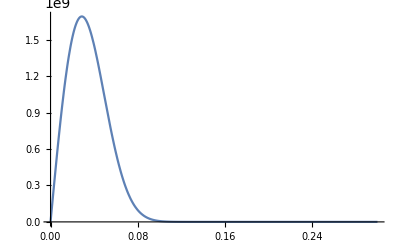

```mathematica
(*as function of q *)
Plot[2500KilogramDay*cfqdRdE[qGeV,30,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1]*(qGeV GeV/(131 mNucleon)),{qGeV,0,0.3},PlotRange->All]
```

```mathematica
func=fqdRdE[qGeV,30]/.{c1p->1,c1n->1,c2p->1,c2n->1,c3p->1,c3n->1,c4p->1,c4n->1,c5p->1,c5n->1,c6p->1,c6n->1,c7p->1,c7n->1,c8p->1,c8n->1,c9p->1,c9n->1,c10p->1,c10n->1,c11p->1,c11n->1,c12p->1,c12n->1,c13p->1,c13n->1,c14p->1,c14n->1,c15p->1,c15n->1};
Plot[2500KilogramDay*func*(qGeV GeV/(131 mNucleon)),{qGeV,0,0.3},PlotRange->All]
```

-Graphics-

Note: E_R = q^2 / 2mT
i.e. q = sqrt( 2*mT*E_R )

Note units of (d R_D)/(d E_R) are “event rate per unit time, per unit detector mass, per unit recoil energy”. Multiplying in the exposure in kilogram days gets “event rate per unit recoil energy”
Note also kinematic threshold E_(R,max)=2(μ_T^2 v^2)/m_T, with μ_T=(m_χ m_T)/(m_χ+m_T)(I assume).

```mathematica
fEdRdE[10^-9,mχ,mT/GeV]/.{c4n->1}/.resttozero
```

1.22459×10^-53

```mathematica
ERmax = 2(μT^2 v^2)/mT/GeV/.v->ve
```

0.0000444707

0.0000444707

0.000249933

1.84085×10^59 CompiledFunction[…][ER,150,122.878,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0]

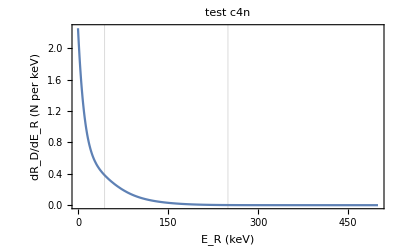

```mathematica
(*as function of E_R *)
mχ=150;(*GeV*)
mT = 131 mNucleon;
μT=(mχ GeV mT)/(mχ GeV+mT);
ERmax = 2(μT^2 v^2)/mT/GeV/.v->ve;(*just using earth speed to get rough number, and get rid of GeV units for plotting*)
ERmaxesc = 2(μT^2 v^2)/mT/GeV/.v->vesc;

resttozero={c1p->0,c1n->0,c2p->0,c2n->0,c3p->0,c3n->0,c4p->0,c4n->0,c5p->0,c5n->0,c6p->0,c6n->0,c7p->0,c7n->0,c8p->0,c8n->0,c9p->0,c9n->0,c10p->0,c10n->0,c11p->0,c11n->0,c12p->0,c12n->0,c13p->0,c13n->0,c14p->0,c14n->0,c15p->0,c15n->0};
arg=2500KilogramDay*fEdRdE[ER,mχ,mT/GeV]/.{c4n->1}/.resttozero
Plot[arg*10^-6/.ER->(10^-6 ERv),{ERv,0 ,500 },Frame->True ,FrameLabel->{"E_R (keV)","dR_D/dE_R (N per keV)"},GridLines->{{ERmax*10^6,ERmaxesc*10^6},{}},PlotLabel->"test c4n",PlotRange->All]
```

```mathematica
arg/.rules⟦1⟧/.resttozero
```

1.84085×10^59 CompiledFunction[…][ER,150,122.878,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0]

{4.8045 GeV,35.5389 GeV,98.6373 GeV}

PlotStyle→-Graphics-

```mathematica
(* Grid *)
mχ={5,10,50,100,500};(*GeV*)
mT = 131 mNucleon;
μT=Table[(mχ⟦i⟧ GeV mT)/(mχ⟦i⟧ GeV+mT),{i,1,Length[mχ]}];
ERmax =Table[ 2(μT⟦i⟧^2 v^2)/mT/GeV/.v->ve,{i,1,Length[mχ]}];(*just using earth speed to get rough number, and get rid of GeV units for plotting*)
ERmaxesc = Table[2(μT⟦i⟧^2 v^2)/mT/GeV/.v->vesc,{i,1,Length[mχ]}];
generalfunc= Table[2500KilogramDay*fEdRdE[ER,mχ⟦i⟧,mT/GeV],{i,1,Length[mχ]}];
curvenames=Table["mχ="<>ToString[mχ⟦i⟧],{i,1,Length[mχ]}]

coefflist={c1p,c1n,c2p,c2n,c3p,c3n,c4p,c4n,c5p,c5n,c6p,c6n,c7p,c7n,c8p,c8n,c9p,c9n,c10p,c10n,c11p,c11n,c12p,c12n,c13p,c13n,c14p,c14n,c15p,c15n};
resttozero={c1p->0,c1n->0,c2p->0,c2n->0,c3p->0,c3n->0,c4p->0,c4n->0,c5p->0,c5n->0,c6p->0,c6n->0,c7p->0,c7n->0,c8p->0,c8n->0,c9p->0,c9n->0,c10p->0,c10n->0,c11p->0,c11n->0,c12p->0,c12n->0,c13p->0,c13n->0,c14p->0,c14n->0,c15p->0,c15n->0};
Nops=15
rules=Table[{{coefflist⟦2*i-1⟧->1},{coefflist⟦2*i⟧->1},{coefflist⟦2*i-1⟧->1,coefflist⟦2*i⟧->1}},{i,1,Nops}]
Monitor[funcs=Table[Table[Table[generalfunc⟦mWIMP⟧/.rules⟦i⟧⟦p⟧/.resttozero,{mWIMP,1,Length[mχ]}],{p,1,3}],{i,1,Nops}],{i,p,mWIMP}];
titles=Table[{ToString[coefflist⟦2*i-1⟧],ToString[coefflist⟦2*i⟧],ToString[coefflist⟦2*i-1⟧]<>"="<>ToString[coefflist⟦2*i⟧]},{i,1,Nops}]
```

```mathematica
Earr=Table[N[ER*10^-6],{ER,0 ,1000,0.5}];
Monitor[plotdata=Table[Table[Transpose[Join[{Earr*10^6},Table[funcs⟦i⟧⟦p⟧⟦m⟧*10^-6/.ER->Earr,{m,1,Length[mχ]}]]],{p,1,3}],{i,1,15}],{i,p,m}];
```

```mathematica
Dimensions[plotdata]
```

{15,3,6,51}

```mathematica
Do[Do[Export["/home/farmer/mathematica/DMFormFactor_13086288/EFTcoeffplotdata/"<>titles⟦i⟧⟦p⟧<>".dat",plotdata⟦i⟧⟦p⟧,"Table"],{i,1,Nops}],{p,1,3}];
```

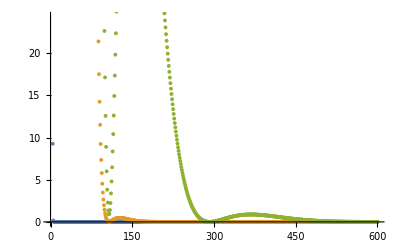

```mathematica
ListPlot[Table[Table[{plotdata⟦1⟧⟦i⟧⟦1⟧,plotdata⟦1⟧⟦i⟧⟦m+1⟧},{i,1,Length[plotdata⟦1⟧]}],{m,1,Length[mχ]}]]
```

```mathematica
plots=Table[
Table[Plot[funcs⟦m⟧⟦i⟧*10^-6/.ER->(10^-6 ERv),{ERv,0 ,500 },Frame->True ,FrameLabel->{"E_R (keV)","dR_D/dE_R (N per keV)"},GridLines->{{ERmax⟦m⟧*10^6,ERmaxesc⟦m⟧*10^6},{}},PlotLabel->titles⟦i⟧,PlotRange->All,PlotPoints->20,MaxRecursion->2,PlotStyle->ColorData[1,"ColorList"]⟦m⟧],{m,1,Length[mχ]}],{i,1,30}];
```

```mathematica
Do[Do[Export["/home/farmer/mathematica/DMFormFactor_13086288/EFTcoeffplotdata/"<>ToString[coefflist⟦i⟧]<>".dat",plotscomb⟦i⟧,"CSV"],{i,1,Nops}],{p,1,3}];
```

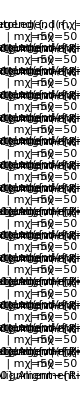

```mathematica
GraphicsGrid[ArrayReshape[plotscomb,{15,2}],ImageSize->Full]
```

```mathematica
Options[legendMaker]=Join[FilterRules[Options[Framed],Except[{ImageSize,FrameStyle,Background,RoundingRadius,ImageMargins}]],{FrameStyle->None,Background->Directive[Opacity[.7],LightGray],RoundingRadius->10,ImageMargins->0,PlotStyle->Automatic,PlotMarkers->None,"LegendLineWidth"->35,"LegendLineAspectRatio"->.3,"LegendMarkerSize"->8,"LegendGridOptions"->{Alignment->Left,Spacings->{.4,.1}}}];


legendMaker::usage="Create a Graphics object with legends given by the list passed as the first argument. The options specify any non-deafult line styles (using PlotStyle -> {...}) or plot markers (using PlotMarkers -> {...}). For more options, inspect Options[legendMaker]";

legendMaker[textLabels_,opts:OptionsPattern[]]:=Module[{f,lineDirectives,markerSymbols,n=Length[textLabels],x},lineDirectives=((PlotStyle/.{opts})/.PlotStyle|Automatic:>Map[ColorData[1],Range[n]])/.None->{None};
markerSymbols=Replace[((PlotMarkers/.{opts})/.Automatic:>(Drop[Normal[ListPlot[Transpose[{Range[3]}],PlotMarkers->Automatic][[1,2]]][[1]],-1]/.Inset[x_,i__]:>x)[[All,-1]])/.{Graphics[gr__],sc_}:>Graphics[gr,ImageSize->("LegendMarkerSize"/.{opts}/.Options[legendMaker,"LegendMarkerSize"]/.{"LegendMarkerSize"->8})],PlotMarkers|None:>Map[Style["",Opacity[0]]&,textLabels]]/.None|{}->Style["",Opacity[0]];
lineDirectives=PadRight[lineDirectives,n,lineDirectives];
markerSymbols=PadRight[markerSymbols,n,markerSymbols];
f=Grid[MapThread[{Graphics[{#1/.None->{},If[#1==={None}||(PlotStyle/.{opts})===None,{},Line[{{-.1,0},{.1,0}}]],Inset[#2,{0,0},Background->None]},AspectRatio->("LegendLineAspectRatio"/.{opts}/.Options[legendMaker,"LegendLineAspectRatio"]/.{"LegendLineAspectRatio"->.2}),ImageSize->("LegendLineWidth"/.{opts}/.Options[legendMaker,"LegendLineWidth"]/.{"LegendLineWidth"->35}),ImagePadding->{{1,1},{0,0}}],Text[#3,FormatType->TraditionalForm]}&,{lineDirectives,markerSymbols,textLabels}],Sequence@Evaluate[("LegendGridOptions"/.{opts}/.Options[legendMaker,"LegendGridOptions"]/.{"LegendGridOptions"->{Alignment->Left,Spacings->{.4,.1}}})]];
Framed[f,FilterRules[{Sequence[opts,Options[legendMaker]]},FilterRules[Options[Framed],Except[ImageSize]]]]];

extractStyles::usage="returns a tuple {\"all line style directives\", \"all plot markers\"} found in the plot, in the order they are drawn. The two sublists need not have the same length if some lines don't use markers ";
extractStyles[plot_]:=Module[{lines,markers,points,extract=First[Normal[plot]]},(*In a plot,the list of lines contains no insets,so I use this to find it:*)lines=Select[Cases[Normal[plot],{___,_Line,___},Infinity],FreeQ[#1,Inset]&];
points=Select[Cases[Normal[plot],{___,_Point,___},Infinity],FreeQ[#1,Inset]&];
(*Most plot markers are inside Inset,except for Point in list plots:*)markers=Select[extract,!FreeQ[#1,Inset]&];
(*The function returns a list of lists:*){(*The first return value is the list of line plot styles:*)Replace[Cases[lines,{c__,Line[__],___}:>Flatten[Directive@@Cases[{c},Except[_Line]]],Infinity],{}->None],(*Second return value:marker symbols*)Replace[Join[Cases[markers,{c__,Inset[s_,pos_,d___],e___}:>If[(*markers "s" can be strings or graphics*)Head[s]===Graphics,(*Append scale factor in case it's needed later;
default 0.01*){s,Last[{.01,d}]/.Scaled[f_]:>First[f]},If[(*For strings,add line color if no color specified via text styles:*)FreeQ[s,CMYKColor|RGBColor|GrayLevel|Hue],Style[s,c],s]],Infinity],(*Filter out Pointsize-legends don't need it:*)Cases[points,{c___,Point[pt__],___}:>{Graphics[{c,Point[{0,0}]}]/.PointSize[_]:>PointSize[1],.01},Infinity]],{}->None]}]

autoLegend::usage="Simplified legending for the plot passed as first argument, with legends given as second argument. Use the option Alignment -> {horizontal, vertical} to place the legend in the PlotRegion in scaled coordinates. For other options, see Options[legendMaker] which are used by autoLegend.";
Options[autoLegend]=Join[{Alignment->{Right,Top},Background->White,AspectRatio->Automatic},FilterRules[Options[legendMaker],Except[Alignment|Background|AspectRatio]]];
autoLegend[plot_Graphics,labels_,opts:OptionsPattern[]]:=Module[{lines,markers,align=OptionValue[Alignment]},{lines,markers}=extractStyles[plot];
Graphics[{Inset[plot,{-1,-1},{Left,Bottom},Scaled[1]],Inset[legendMaker[labels,PlotStyle->lines,PlotMarkers->markers,Sequence@@FilterRules[{opts},FilterRules[Options[legendMaker],Except[Alignment]]]],align,Map[If[NumericQ[#],Center,#]&,align]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->(OptionValue[AspectRatio]/.Automatic:>(AspectRatio/.Options[plot,AspectRatio])/.Automatic:>(AspectRatio/.AbsoluteOptions[plot,AspectRatio]))]]
```